```mathematica
Jhop = 1000;
δ=-0.1;
Jplus=Jhop(1+δ);
Jminus=Jhop(1-δ);
Clear[Jplus, Jminus];
M=({{0, Jplus, Jplus+Jminus E^(I ky)}, {Jplus, 0, 0}, {Jplus+Jminus E^(-I ky), 0, 0}});
J = ({{0, 0, 0}, {Jminus, 0, 0}, {0, 0, 0}});
{V,Ξ,W} = SingularValueDecomposition[J];
r = MatrixRank[Ξ];
V = V[[All,1;;r]];
W = W[[All,1;;r]];
Ξ=DiagonalMatrix[Diagonal[Ξ][[1;;r]]];
𝒢=Simplify@Inverse[ϵ IdentityMatrix[3]-M];
𝒢vv=Simplify[V†.𝒢.V];
𝒢vw=Simplify[W†.𝒢.V];
𝒢wv=Simplify[V†.𝒢.W];
𝒢ww=Simplify[W†.𝒢.W];
T=PowerExpand@Assuming[{Jplus, Jminus,ky}>0,Simplify[Join[Simplify@Join[Inverse[Ξ].Inverse[𝒢vw],-Inverse[Ξ].Inverse[𝒢vw].𝒢ww.Ξ,2],Simplify@Join[𝒢vv.Inverse[𝒢vw],(𝒢wv-𝒢vv.Inverse[𝒢vw].𝒢ww).Ξ,2]]]];
Δ=Tr[TrigExpand[FullSimplify[T]]];
Δ
```

-(2 Jminus)/Jplus-(2 Jplus)/Jminus+ϵ^2/(Jminus Jplus)-2 Cos[ky]

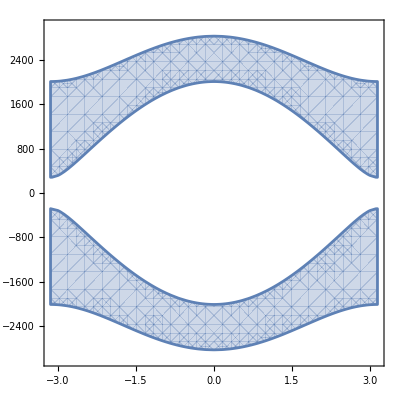

```mathematica
RegionPlot[Abs[Δ]<=2,{ky,-π,π},{ϵ,-3Jhop,3Jhop}]
```

```mathematica
𝒥=({{0, 1}, {-1, 0}});Φ1=({{1}, {0}});ΦN=({{0}, {1}});
Show[ContourPlot[Simplify[First@Flatten[Transpose[Φ1].𝒥.T.Φ1,3]]==0,{ky,-π,π},{ϵ,-3Jhop,3Jhop},ColorFunction->Hue],RegionPlot[Abs[Δ]<=2,{ky,-π,π},{ϵ,-3Jhop,3Jhop}],ContourPlot[Simplify[First@Flatten[Transpose[ΦN].𝒥.T.ΦN,3]]==0,{ky,-π,π},{ϵ,-3Jhop,3Jhop},ColorFunction->(Blue&)]]
```

-Graphics-

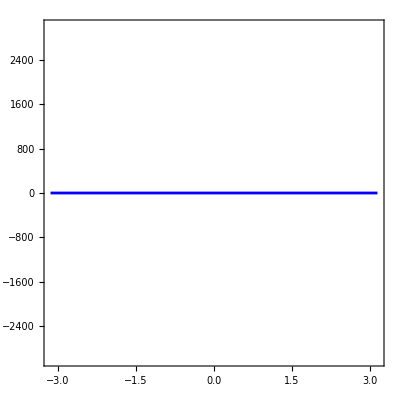

```mathematica
ContourPlot[Simplify[First@Flatten[Transpose[ΦN].𝒥.T.ΦN,3]]==0,{ky,-π,π},{ϵ,-3Jhop,3Jhop},ColorFunction->(Blue&)]
```

```mathematica
ContourPlot[Simplify[First@Flatten[Transpose[Φ1].𝒥.T.Φ1,3]]==0,{ky,-π,π},{ϵ,-3Jhop,3Jhop},ColorFunction->Hue]
```

-Graphics-

```mathematica
Simplify[First@Flatten[Transpose[ΦN].𝒥.T.ΦN,3]]==0
```

(ϵ Abs[Jminus])/(Jminus Jplus)==0

```mathematica
Assuming[{Jplus,Jminus}>0,FullSimplify@PowerExpand@First@Flatten[Transpose[Φ1].𝒥.T.Φ1,3]==0]
```

-((Jminus^2+Jplus^2-ϵ^2+2 Jminus Jplus Cos[ky]) Sign[Jminus])/(Jplus ϵ)==0

```mathematica
ΦN
```

{{0},{1}}

```mathematica
Assuming[{Jplus,Jminus}>0,T.ΦN//PowerExpand]//FullSimplify
```

{{-ϵ/(Jplus Sign[Jminus])},{-(Conjugate[Jminus]^(3/2) Sign[Jminus])/(√Jminus Jplus)}}

```mathematica
FullSimplify@(FullSimplify@T/.{ky->ArcCos[(-Jplus^2-Jminus^2)/(2Jplus Jminus)]})/.{ϵ->0}//MatrixForm
```

Power::infy: 碰到无穷表达式 1/0.

(-0.818182-4.94807×10^-17 ⅈ | 0.
ComplexInfinity | -1.22222)

```mathematica
ArcCos[1.2]
```

0.+0.622363 ⅈ

```mathematica
Assuming[{Jplus,Jminus}>0,T]//FullSimplify//MatrixForm
```

(-(Jminus^2+2 Jplus^2-ϵ^2+2 Jminus Jplus Cos[ky])/(Jminus Jplus) | -ϵ/(Jplus Sign[Jminus])
-((Jminus^2+Jplus^2-ϵ^2+2 Jminus Jplus Cos[ky]) Sign[Jminus])/(Jplus ϵ) | -Jminus/Jplus)

```mathematica
Assuming[{Jplus,Jminus}>0,Eigenvalues[T]]//FullSimplify
```

{1/(2 Jminus^2 Jplus^3 ϵ)(Jminus Jplus^2 ϵ (-2 (Jminus^2+Jplus^2)+ϵ^2-2 Jminus Jplus Cos[ky])-ⅇ^(-2 ⅈ ky) √(ⅇ^(4 ⅈ ky) Jminus^2 Jplus^4 ϵ^2 (4 Jminus^4+Jminus^2 (6 Jplus^2-4 ϵ^2)+(-2 Jplus^2+ϵ^2)^2+2 Jminus Jplus ((4 (Jminus^2+Jplus^2)-2 ϵ^2) Cos[ky]+Jminus Jplus Cos[2 ky])))),1/(2 Jminus^2 Jplus^3 ϵ)(Jminus Jplus^2 ϵ (-2 (Jminus^2+Jplus^2)+ϵ^2-2 Jminus Jplus Cos[ky])+ⅇ^(-2 ⅈ ky) √(ⅇ^(4 ⅈ ky) Jminus^2 Jplus^4 ϵ^2 (4 Jminus^4+Jminus^2 (6 Jplus^2-4 ϵ^2)+(-2 Jplus^2+ϵ^2)^2+2 Jminus Jplus ((4 (Jminus^2+Jplus^2)-2 ϵ^2) Cos[ky]+Jminus Jplus Cos[2 ky]))))}